{{y→InterpolatingFunction[…]}}

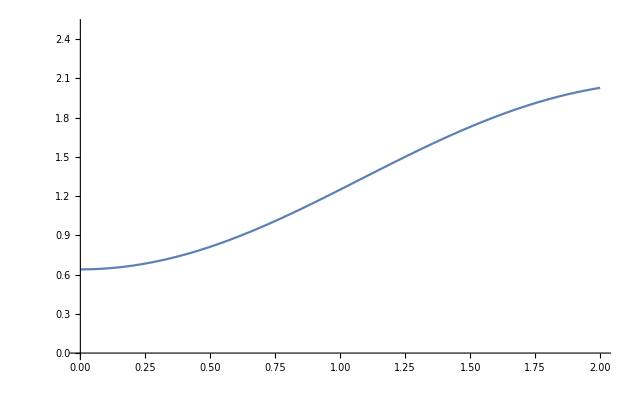

{0.819367}

```mathematica
sol=NDSolve[{-(-5Cos[y[t]]*(y'[t])^2-5Sin[y[t]]*y''[t])==(0.1-Cot[y[t]])*(-5Sin[y[t]]*(y'[t])^2+5Cos[y[t]]*y''[t])-2+10Cot[y[t]],y[0]==0.64,y'[0]==0},y,{t,0,10}]
Plot[Evaluate[y[t]/.sol],{t,0,2},PlotRange->{0,2.5}]
Evaluate[y'[0.65351]/.sol]
```

```mathematica
ArcSin[4/5]
```

ArcSin[4/5]

```mathematica
N[ArcSin[4/5]]
```

0.927295

```mathematica
Sin[y[t]]/Norm[Sin[y[t]]]
```

```mathematica
-3*0.8193665346176673
```

-2.4581

```mathematica
0.5*2.5*(2.458099603853002)^2
```

7.55282

```mathematica
NumberForm[-3.2756,16]
```

```mathematica
-4*0.8193665346176673
```

-3.27747

```mathematica
3.2756
```

```mathematica
0.5*2.5*(3.277466138470669)^2
```

13.4272

```mathematica
DSolve[-(-5(1-0.5(y[t])^2)*(y'[t])^2-5(y[t]-1/6(y[t])^3)*y''[t])==(0.1-(1-0.5(y[t])^2)/y[t])*(-5(y[t])*(y'[t])^2+5(1-0.5(y[t])^2)*y''[t])-2+10(1-0.5(y[t])^2)/y[t],y,t]
```

$Aborted

```mathematica
(1-0.5(y[t])^2)
```

```mathematica
(y[t]-1/6(y[t])^3)
```

```mathematica
ArcCos[2/5]
```

ArcCos[2/5]

```mathematica
N[ArcCos[-2/5]]
```

1.98231